```mathematica
h((1-x)+(1-c)(a(1-x)+b(x-c))+k Log[1/x]-p Log[1/x]-r Log[x/c])+j(p(1-x)+l(1-c))-c(k)
```

```mathematica
(h(1-x))/(2c)== k
```

```mathematica
x== (h*p+g*a)/(k-p)
```

```mathematica
g/(2c)Log[1/x]== k
```

```mathematica
Solve[g/(2c)Log[1/x]==(h(1-x))/(2c),x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→-(g ProductLog[-(ⅇ^(-h/g) h)/g])/h}}

```mathematica
Solve[x== (h*p+g*a)/((h(1-x))/(2c)-p),x]
```

{{x→(h-2 c p-√((-h+2 c p)^2-4 h (2 a c g+2 c h p)))/(2 h)},{x→(h-2 c p+√((-h+2 c p)^2-4 h (2 a c g+2 c h p)))/(2 h)}}

```mathematica
Simplify[Solve[g/(2c)Log[1/(-(g ProductLog[-(ⅇ^(-h/g) h)/g])/h)]== k,k]]
```

{{k→(g Log[-h/(g ProductLog[-(ⅇ^(-h/g) h)/g])])/(2 c)}}

```mathematica
Manipulate[Plot[]]
```

```mathematica
Solve[x== (h*p+g*a)/(g/(2c)Log[1/x]-p),x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→-(2 (a c g+c h p))/(g ProductLog[-(2 c ⅇ^((2 c p)/g) (a g+h p))/g])}}

```mathematica
Manipulate[Plot[(h-2  p+√((-h+2  p)^2-4* h *(2 *a *g+2 * h* p)))/(2 h),{p,0,100}],{h,0,1},{g,0,1},{a,1,100}]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

```mathematica
D[-k + k*Log[(a-1)√(1-r)]-k*Log[p-r-k]-r*Log[p-r-k]-c*k^2,k]
```

-1-2 c k+k/(-k+p-r)+r/(-k+p-r)+Log[(-1+a) √(1-r)]-Log[-k+p-r]

```mathematica
Solve[%==0,k]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

```mathematica
Solve[-1-2 c k+k/(-k+p-r)+r/(-k+p-r)+Log[(-1+a) √(1-r)]==0,k]
```

{{k→-1/(4 c)(2-2 c p+2 c r-Log[(-1+a) √(1-r)]+√((-2+2 c p-2 c r+Log[(-1+a) √(1-r)])^2+8 c (p-2 r-p Log[(-1+a) √(1-r)]+r Log[(-1+a) √(1-r)])))},{k→1/(4 c)(-2+2 c p-2 c r+Log[(-1+a) √(1-r)]+√((-2+2 c p-2 c r+Log[(-1+a) √(1-r)])^2+8 c (p-2 r-p Log[(-1+a) √(1-r)]+r Log[(-1+a) √(1-r)])))}}

```mathematica
D[^2,k]
```

```mathematica
-k + k*Log[(a-1)√(1-r)]-k*Log[p-r-k]-r*Log[p-r-k]-c*k
```

```mathematica
Simplify[D[(a-1)(√(1-r))(1-√(1-r)),r]]
```

```mathematica
((-1+a) (-1+2 √(1-r)))/(2 √(1-r))
```

((-1+a) (-1+2 √(1-r)))/(2 √(1-r))

```mathematica
ⅇ^(Log[(a-1)√(1-r)]-2)+r
```

```mathematica
Manipulate[Plot[ⅇ^(Log[(a-1)√(1-r)]-2)+r,{r,0,1}],{a,1,20}]
```

```mathematica
D[a/(2 √(1-r))-p/(2(1-r))-3-Log[p-r-k]+Log[(a-1)√(1-r)(1-√(1-r))]+(r(2 √(1-r)-1))/(2(1-r)(1-√(1-r))),r]
```

-p/(2 (1-r)^2)+a/(4 (1-r)^(3/2))+(-1+2 √(1-r))/(2 (1-√(1-r)) (1-r))+(1/2 (-1+a)-((-1+a) (1-√(1-r)))/(2 √(1-r)))/((-1+a) (1-√(1-r)) √(1-r))+1/(-k+p-r)+((-1+2 √(1-r)) r)/(2 (1-√(1-r)) (1-r)^2)-r/(2 (1-√(1-r)) (1-r)^(3/2))-((-1+2 √(1-r)) r)/(4 (1-√(1-r))^2 (1-r)^(3/2))

```mathematica
Manipulate[Plot[-p/(2 (1-r)^2)+a/(4 (1-r)^(3/2))+(-1+2 √(1-r))/(2 (1-√(1-r)) (1-r))+(1/2 (-1+a)-((-1+a) (1-√(1-r)))/(2 √(1-r)))/((-1+a) (1-√(1-r)) √(1-r))+1/(-k+p-r)+((-1+2 √(1-r)) r)/(2 (1-√(1-r)) (1-r)^2)-r/(2 (1-√(1-r)) (1-r)^(3/2))-((-1+2 √(1-r)) r)/(4 (1-√(1-r))^2 (1-r)^(3/2)),{r,0,1}],{p,0,5},{k,0,0},{a,1.1,20}]
```

```mathematica
Manipulate[Plot[-(ⅇ^(Log[(a-1)√(1-r)]-2)+r)/(2 (1-r)^2)+a/(4 (1-r)^(3/2))+(-1+2 √(1-r))/(2 (1-√(1-r)) (1-r))+(1/2 (-1+a)-((-1+a) (1-√(1-r)))/(2 √(1-r)))/((-1+a) (1-√(1-r)) √(1-r))+1/ⅇ^(Log[(a-1)√(1-r)]-2)+((-1+2 √(1-r)) r)/(2 (1-√(1-r)) (1-r)^2)-r/(2 (1-√(1-r)) (1-r)^(3/2))-((-1+2 √(1-r)) r)/(4 (1-√(1-r))^2 (1-r)^(3/2)),{r,0,1}],{p,0,5},{k,0,0},{a,1.1,20}]
```

```mathematica
Simplify[-(ⅇ^(Log[(a-1)√(1-r)]-2)+r)/(2 (1-r)^2)+a/(4 (1-r)^(3/2))+(-1+2 √(1-r))/(2 (1-√(1-r)) (1-r))+(1/2 (-1+a)-((-1+a) (1-√(1-r)))/(2 √(1-r)))/((-1+a) (1-√(1-r)) √(1-r))+1/ⅇ^(Log[(a-1)√(1-r)]-2)+((-1+2 √(1-r)) r)/(2 (1-√(1-r)) (1-r)^2)-r/(2 (1-√(1-r)) (1-r)^(3/2))-((-1+2 √(1-r)) r)/(4 (1-√(1-r))^2 (1-r)^(3/2))==0]
```

(2 (-1+r) (-2+2 √(1-r)+r)-a^2 (-2+ⅇ^2) (-1+r) (-2+2 √(1-r)+r)+4 ⅇ^4 (-1+r)^2 (-2+2 √(1-r)+r)+ⅇ^2 (-12 (-1+√(1-r))+5 (-3+2 √(1-r)) r+(3-2 √(1-r)) r^2)+2 a (-2 (-1+r) (-2+2 √(1-r)+r)+ⅇ^2 (5 (-1+√(1-r))+(6-4 √(1-r)) r+(-1+√(1-r)) r^2)))/((-1+a) (-1+√(1-r)) √(1-r))==0

```mathematica
Solve[%,r]
```

$Aborted

```mathematica
S== a √(1-r)+p-2*r-k+1+k*Log[(a-1)√(1-r)]-k*Log[p-r-k]-p*Log[(a-1)√(1-r)]+p*Log[p-r-k]-r*Log[p-r-k]+r*Log[(a-1)√(1-r)(1-√(1-r))]
```

```mathematica
S== a √(1-r)+p-2*r-1-p*Log[(a-1)√(1-r)]+p*Log[p-r]-r*Log[p-r]+r*Log[(a-1)√(1-r)(1-√(1-r))]
```

```mathematica
ⅇ^(Log[(a-1)√(1-r)]-2)+r
```

```mathematica
S== a √(1-r)+ⅇ^(Log[(a-1)√(1-r)]-2)+r-2*r-1-ⅇ^(Log[(a-1)√(1-r)]-2)+r*Log[(a-1)√(1-r)]+ⅇ^(Log[(a-1)√(1-r)]-2)+r*Log[ⅇ^(Log[(a-1)√(1-r)]-2)]-r*Log[ⅇ^(Log[(a-1)√(1-r)]-2)]+r*Log[(a-1)√(1-r)(1-√(1-r))]
```

```mathematica
Manipulate[Plot[ a √(1-r)+ⅇ^(Log[(a-1)√(1-r)]-2)+r-2*r-1-ⅇ^(Log[(a-1)√(1-r)]-2)+r*Log[(a-1)√(1-r)]+ⅇ^(Log[(a-1)√(1-r)]-2)+r*Log[ⅇ^(Log[(a-1)√(1-r)]-2)]-r*Log[ⅇ^(Log[(a-1)√(1-r)]-2)]+r*Log[(a-1)√(1-r)(1-√(1-r))],{r,0,1}],{a,1,20}]
```

```mathematica
Manipulate[Plot[ a √(1-r)+ⅇ^(Log[(a-1)√(1-r)]-2)-r(1+Log[ⅇ^Log[(a-1)√(1-r)-2]]-Log[(a-1)√(1-r)](1-√(1-r)))+1
-2(ⅇ^(Log[(a-1)√(1-r)]-2)+r),{r,0,1}],{a,1,20}]
```

```mathematica
Manipulate[Plot[ a √(1-r)+ⅇ^(Log[(a-1)√(1-r)]-2)-r(1+Log[(a-1)√(1-r)-2]-Log[(a-1)√(1-r)](1-√(1-r)))+1
-2(ⅇ^(Log[(a-1)√(1-r)]-2)+r),{r,0,1}],{a,1,20}]
```

```mathematica
ToExpression["10*sqrt(1-x) 
-exp(ln((10-1)*sqrt(1-x))-2) 
-x(1+ln((10-1)*sqrt(1-x)-2)-ln((10-1)*sqrt(1-x))*(1-sqrt(1-x)))
+1
-2(exp(ln((10-1)*sqrt(1-x))-2)+x)",TeXForm]
```

1-e x p[-2+l n[9 q r $Failed t[1-x]]]-2 (x+e x p[-2+l n[9 q r $Failed t[1-x]]])+10 q r $Failed t[1-x]-x[1+l n[-2+9 q r $Failed t[1-x]]-l n[9 q r $Failed t[1-x]] (1-q r $Failed t[1-x])]

```mathematica
TeXForm[a √(1-r)+ⅇ^(Log[(a-1)√(1-r)]-2)-r(1+Log[(a-1)√(1-r)-2]-Log[(a-1)√(1-r)](1-√(1-r)))+1
-2(ⅇ^(Log[(a-1)√(1-r)]-2)+r)]
```

\frac{(a-1) \sqrt{1-r}}{e^2}-2 \left(\frac{(a-1)
   \sqrt{1-r}}{e^2}+r\right)+a \sqrt{1-r}-r \left(\log
   \left((a-1) \sqrt{1-r}-2\right)-\left(1-\sqrt{1-r}\right) \log
   \left((a-1) \sqrt{1-r}\right)+1\right)+1

```mathematica
profit== (2*(r+k)+(a-1)√(1-r))/4-((a-1)^2(1-r)-(2(r+k))^2)/(8(a-1)√(1-r))+(l(√(1-r)))/2-k^2
```

```mathematica
p == ((r+(a-1)√(1-r))((a-1)(√(1-r))4-1))/((a-1)√(1-r))
```

```mathematica
k == ((r+(a-1)√(1-r))((a-1)(√(1-r))4-1))/((a-1)^2(1-r))
```

```mathematica
(2*(r+k)+(a-1)√(1-r))/4-((a-1)^2(1-r)-(2(r+k))^2)/(8(a-1)√(1-r))+(l(√(1-r)))/2-k^2
```

```mathematica
Manipulate[Plot[ (12m-4)/(4m-1)^2(r+m)^2+l √(1-r)-((r+m)/(m4-1))^2,{r,0,1}],{a,1.1,5},{l,0,10}]
```

```mathematica
m == (a-1)√(1-r)
```

```mathematica
Manipulate[Plot[ (12((a-1)√(1-r))-4)/(4((a-1)√(1-r))-1)^2(r+((a-1)√(1-r)))^2+l √(1-r)-((r+((a-1)√(1-r)))/(((a-1)√(1-r))4-1))^2,{r,0,1}],{a,1.1,2},{l,0,10}]
```

```mathematica
Solve[D[(12((a-1)√(1-r))-4)/(4((a-1)√(1-r))-1)^2(r+((a-1)√(1-r)))^2+l √(1-r)-((r+((a-1)√(1-r)))/(((a-1)√(1-r))4-1)),r]==0,r]
```

$Aborted

```mathematica
(r+((a-1)√(1-r)))/(((a-1)√(1-r))4-1)
```

```mathematica
Manipulate[Plot[ (r+((a-1)√(1-r)))/(((a-1)√(1-r))4-1),{r,0,1}],{a,1.1,2}]
```

```mathematica
Solve[((r+(a-1)√(1-r))((a-1)(√(1-r))4-1))/((a-1)√(1-r))((((r+(a-1)√(1-r))((a-1)(√(1-r))4-1))/((a-1)√(1-r))-r-((r+(a-1)√(1-r))((a-1)(√(1-r))4-1))/((a-1)^2(1-r)))/(2(a-1)(1-r)))+(((r+(a-1)√(1-r))((a-1)(√(1-r))4-1))/((a-1)√(1-r)))/(a-1)+l==0,r]
```

$Aborted

```mathematica
Manipulate[Plot[(r+(a-1)√(1-r))/(4((a-1)√(1-r))-1)(2((a-1)√(1-r))-1)-r,{r,0,1}],{a,1.00001,5}]
```

```mathematica
Manipulate[Plot[1/(√(1-r))-(((r+(a-1)√(1-r))((a-1)(√(1-r))4-1))/((a-1)√(1-r))-r-((r+(a-1)√(1-r))((a-1)(√(1-r))4-1))/((a-1)^2(1-r)))/(a-1),{r,0,1}],{a,1.000001,10}]
```

```mathematica
p == ((r+(a-1)√(1-r))((a-1)(√(1-r))4-1))/((a-1)√(1-r))
```

```mathematica
k == ((r+(a-1)√(1-r))((a-1)(√(1-r))4-1))/((a-1)^2(1-r))
```

```mathematica
Plot[√(1-r)-(1-(p-r-k)/((a-1)√(1-r))),{r,0,1}],{a,1.000001,10}]
```

```mathematica
Manipulate[Plot[√(1-r)-(1-(((r+(a-1)√(1-r))((a-1)(√(1-r))4-1))/((a-1)√(1-r))-r-((r+(a-1)√(1-r))((a-1)(√(1-r))4-1))/((a-1)^2(1-r)))/((a-1)√(1-r))),{r,0,1}],{a,1.000001,10}]
```

```mathematica
(12m-4)/(4m-1)(r+m)^2+l √(1-r)-((r+m)/(m4-1))^2
```

```mathematica
l √(1-r)-((r+m)/(m4-1))^2
```

```mathematica
(m(4r+1))/(4m-1)(r+m)^2+l √(1-r)-((r+m)/(m4-1))^2
```

```mathematica
Manipulate[Plot[{(12m-4)/(4m-1)(r+m)^2+l √(1-r)-((r+m)/(m4-1))^2,l √(1-r)-((r+m)/(m4-1))^2,(m(4r+1))/(4m-1)(r+m)^2+l √(1-r)-((r+m)/(m4-1))^2},{r,0,1}],{a,1.0001,10},{l,0,10}]
```

```mathematica
(a-1)√(1-r)
```

```mathematica
Manipulate[Plot[{(12(a-1)√(1-r)-4)/(4(a-1)√(1-r)-1)(r+(a-1)√(1-r))^2+l √(1-r)-((r+(a-1)√(1-r))/((a-1)√(1-r)4-1))^2,l √(1-r)-((r+(a-1)√(1-r))/((a-1)√(1-r)4-1))^2,((a-1)√(1-r)(4r+1))/(4(a-1)√(1-r)-1)(r+(a-1)√(1-r))^2+l √(1-r)-((r+(a-1)√(1-r))/((a-1)√(1-r)4-1))^2},{r,0,.25}],{a,1.0001,5},{l,0,100}]
```

```mathematica
Manipulate[Plot[{l √(1-r)-((r+(a-1)√(1-r))/((a-1)√(1-r)4-1))^2,((a-1)√(1-r)(4r+1))/(4(a-1)√(1-r)-1)(r+(a-1)√(1-r))^2+l √(1-r)-((r+(a-1)√(1-r))/((a-1)√(1-r)4-1))^2},{r,0,1}],{a,1.0001,5},{l,0,10}]
```

```mathematica
p == ((r+(a-1)√(1-r))(2*(a-1)*(√(1-r))))/((a-1)4 √(1-r)-1)
```

```mathematica
k == (r+(a-1)√(1-r))/((a-1)4 √(1-r)-1)
```

```mathematica
Manipulate[Plot[{((r+(a-1)√(1-r))(2*(a-1)*(√(1-r))))/((a-1)4 √(1-r)-1),(r+(a-1)√(1-r))/((a-1)4 √(1-r)-1)},{r,0,1}],{a,2,10}]
```

```mathematica
Manipulate[Plot[{((r+(a-1)√(1-r))(2*(a-1)*(√(1-r))))/((a-1)4 √(1-r)-1)},{r,0,1}],{a,1.01,100}]
```

```mathematica
a== 1+1/(4*√(1-r))+0.001
```

```mathematica
Manipulate[Plot[{((r+(a-1)√(1-r))(2*(a-1)*(√(1-r))))/((a-1)4 √(1-r)-1)},{r,0,1}],{a,1.25,4}]
```

```mathematica
Solve[2*(a-1)√(1-r)+2r-1==0,r]
```

{{r→1/2 (2 a-a^2-√(3-8 a+8 a^2-4 a^3+a^4))},{r→1/2 (2 a-a^2+√(3-8 a+8 a^2-4 a^3+a^4))}}

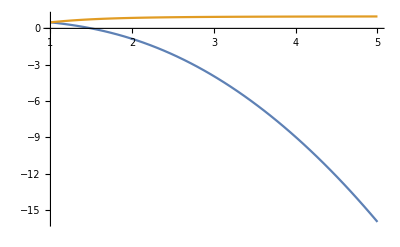

```mathematica
Plot[{1/2 (2 a-a^2-√(3-8 a+8 a^2-4 a^3+a^4)),1/2 (2 a-a^2+√(3-8 a+8 a^2-4 a^3+a^4))},{a,1.001,5}]
```

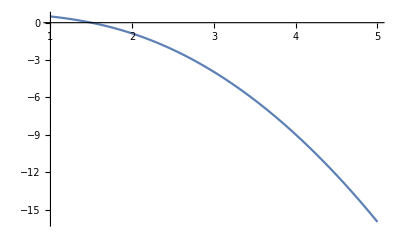

```mathematica
Plot[{1/2 (2 a-a^2-√(3-8 a+8 a^2-4 a^3+a^4))},{a,1.001,5}]
```

```mathematica
Manipulate[Plot[2*(a-1)√(1-r)+2r-1,{r,0,.25}],{a,1.7,5}]
```

```mathematica
Manipulate[Plot[((a-1)√(1-r)-2r)/(2-(a-1)√(1-r)),{r,0,1}],{a,1.1,10}]
```

```mathematica
Manipulate[Plot[{(a-1)√(1-r)-2r,(a-1)√(1-r)-1},{r,0,1}],{a,1.1,10}]
```

```mathematica
Solve[{D[p(((a-1)/a+√(1/a*((1+a)^2/a-4p+4k)))/2)+l(((a-1)/a+√(1/a*((1+a)^2/a-4p+4k)))/2)-k^2,p]==0,D[p(((a-1)/a+√(1/a*((1+a)^2/a-4p+4k)))/2)+l(((a-1)/a+√(1/a*((1+a)^2/a-4p+4k)))/2)-k^2,k]==0},{p,k}]
```

$Aborted

```mathematica
Manipulate[Plot3D[p*(((a-1)/a+√(1/a*((1+a)^2/a-4p+4k)))/2)+l(((a-1)/a+√(1/a*((1+a)^2/a-4p+4k)))/2)-k^2,{k,0,5},{p,0,10}],{a,1,10},{l,0,10}]
```

```mathematica
Solve[{D[p(((a-1)/a+√(1/a*((1+a)^2/a-4p+4k)))/2)+l(((a-1)/a+√(1/a*((1+a)^2/a-4p+4k)))/2)-k^2,k]==0},k]
```

```mathematica
Manipulate[Plot[P(((a-1)/a-√(1/a*((1+a)^2/a-4p)))/2)+l(((a-1)/a-√(1/a*((1+a)^2/a-4p)))/2),{p,0,5}],{a,1,10},{l,0,100}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

```mathematica
k= Solve[D[a*√(1-r)+p-2*r-k+1+k*Log[a-1]+k*Log[√(1-r)]-k*Log[p-r-k]-p*Log[a-1]-p*Log[√(1-r)]+p*Log[p-r-k]-r*Log[p-r-k]+r*Log[a-1]+r*Log[√(1-r)]+r*Log[1-√(1-r)]+p*(1-(p-r-k)/((a-1)√(1-r)))+l*(√(1-r))-k^2,k]==0,k]
```

```mathematica
p=Solve[D[a*√(1-r)+p-2*r-k+1+k*Log[a-1]+k*Log[√(1-r)]-k*Log[p-r-k]-p*Log[a-1]-p*Log[√(1-r)]+p*Log[p-r-k]-r*Log[p-r-k]+r*Log[a-1]+r*Log[√(1-r)]+r*Log[1-√(1-r)]+p*(1-(p-r-k)/((a-1)√(1-r)))+l*(√(1-r))-k^2,p]==0,p]
Clear[p]
```

```mathematica
Manipulate[Plot3D[a*√(1-r)+p-2*r-k+1+k*Log[a-1]+k*Log[√(1-r)]-k*Log[p-r-k]-p*Log[a-1]-p*Log[√(1-r)]+p*Log[p-r-k]-r*Log[p-r-k]+r*Log[a-1]+r*Log[√(1-r)]+r*Log[1-√(1-r)]+p*(1-(p-r-k)/((a-1)√(1-r)))+l*(√(1-r))-k^2,{r,0.000001,0.9999999},{p,0,10},PlotRange->{0,20}],{k,0,0.5},{l,0,10},{a,1.5,20}]
```

```mathematica
Plot3D[x Exp[-x^2-y^2],{x,-2,2},{y,-2,2},PlotRange->{-.3,.3},ClippingStyle->None]
```

```mathematica
D[a*√(1-r)+p-2*r-k+1+k*Log[a-1]+k*Log[√(1-r)]-k*Log[p-r-k]-p*Log[a-1]-p*Log[√(1-r)]+p*Log[p-r-k]-r*Log[p-r-k]+r*Log[a-1]+r*Log[√(1-r)]+r*Log[1-√(1-r)]+p*(1-(p-r-k)/((a-1)√(1-r)))+l*(√(1-r))-k^2,r]
```

-2+p (1/((-1+a) √(1-r))-(-k+p-r)/(2 (-1+a) (1-r)^(3/2)))-k/(2 (1-r))+p/(2 (1-r))-a/(2 √(1-r))-l/(2 √(1-r))+k/(-k+p-r)-p/(-k+p-r)-r/(2 (1-r))+r/(2 (1-√(1-r)) √(1-r))+r/(-k+p-r)+Log[-1+a]+Log[1-√(1-r)]+Log[√(1-r)]-Log[-k+p-r]

```mathematica
Manipulate[Plot[-2+p (1/((-1+a) √(1-r))-(-k+p-r)/(2 (-1+a) (1-r)^(3/2)))-k/(2 (1-r))+p/(2 (1-r))-a/(2 √(1-r))-l/(2 √(1-r))+k/(-k+p-r)-p/(-k+p-r)-r/(2 (1-r))+r/(2 (1-√(1-r)) √(1-r))+r/(-k+p-r)+Log[-1+a]+Log[1-√(1-r)]+Log[√(1-r)]-Log[-k+p-r],{r,0,1}],{a,1.001,10},{k,0,5},{l,0,5},{p,0,5}]
```

```mathematica
D[-2+p (1/((-1+a) √(1-r))-(-k+p-r)/(2 (-1+a) (1-r)^(3/2)))-k/(2 (1-r))+p/(2 (1-r))-a/(2 √(1-r))-l/(2 √(1-r))+k/(-k+p-r)-p/(-k+p-r)-r/(2 (1-r))+r/(2 (1-√(1-r)) √(1-r))+r/(-k+p-r)+Log[-1+a]+Log[1-√(1-r)]+Log[√(1-r)]-Log[-k+p-r],a]
```

1/(-1+a)+p (-1/((-1+a)^2 √(1-r))+(-k+p-r)/(2 (-1+a)^2 (1-r)^(3/2)))-1/(2 √(1-r))

```mathematica
Manipulate[Plot[1/(-1+a)+p (-1/((-1+a)^2 √(1-r))+(-k+p-r)/(2 (-1+a)^2 (1-r)^(3/2)))-1/(2 √(1-r)),{r,0.00001,0.99999}],{a,1.5,8},{k,0,2},{p,0,2}]
```

```mathematica
Simplify[1/(-1+a)+p (-1/((-1+a)^2 √(1-r))+(-k+p-r)/(2 (-1+a)^2 (1-r)^(3/2)))-1/(2 √(1-r))]
```

1/(-1+a)-1/(2 √(1-r))+(p (-2-k+p+r))/(2 (-1+a)^2 (1-r)^(3/2))

```mathematica
D[-2+p (1/((-1+a) √(1-r))-(-k+p-r)/(2 (-1+a) (1-r)^(3/2)))-k/(2 (1-r))+p/(2 (1-r))-a/(2 √(1-r))-l/(2 √(1-r))+k/(-k+p-r)-p/(-k+p-r)-r/(2 (1-r))+r/(2 (1-√(1-r)) √(1-r))+r/(-k+p-r)+Log[-1+a]+Log[1-√(1-r)]+Log[√(1-r)]-Log[-k+p-r],k]
```

p/(2 (-1+a) (1-r)^(3/2))-1/(2 (1-r))+k/(-k+p-r)^2-p/(-k+p-r)^2+2/(-k+p-r)+r/(-k+p-r)^2

```mathematica
Manipulate[Plot[p/(2 (-1+a) (1-r)^(3/2))-1/(2 (1-r))+k/(-k+p-r)^2-p/(-k+p-r)^2+2/(-k+p-r)+r/(-k+p-r)^2,{r,0.00001,0.99999}],{a,1.5,8},{k,0,2},{p,0,2}]
```